```mathematica
Enter the Mathematica  package that generates an autoreggressive price sequence.
```

```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Math\SizePower\SizePower.m
```

```mathematica
(*  The function PriceSequenceGraph[c, p0, p*, n, σ] displays   *)
(*  a sequence of length 'n' that is autoregressive with the    *)
(*  form p[t+1] = p[t] + c *(p* - p[t]) + e[t].  The          *)
(*  adjustment rate is 'c', the initial price is p0 and the     *)
(*  central tendancy is p*.  The dashed line in the graph       *)
(*  shows the level p* that the function reverts to if c > 0.   *)
(*  The random terms are independent and identically            *)
(*  distributed normal random variables with a mean of 0        *)
(*  and variance σ^2.                                           *)
```

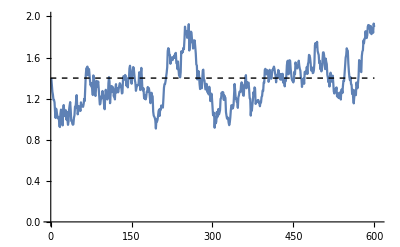

```mathematica
PriceSequenceGraph[0.02, 1.4, 1.4, 600, 0.06]
```

#### In the notebook Size.nb we determined the adjustment rate between the dollar and pound from 1971 through the end of 2020. In this notebook we will examine the power of our tests for adjustment.

```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Data\BRLpCADpGBPpJPYpMXNpNOKpTRLpUSD.txt;
```

```mathematica
Off[General::munfl]
```

```mathematica
cEsttStat[Transpose[USDpGBP][[2]], 1]
```

{0.0194004,2.60878,1.42006}

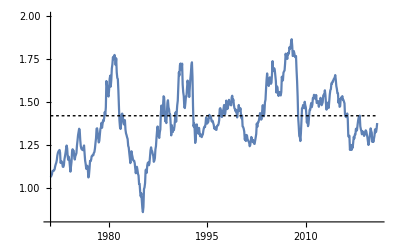

```mathematica
Show[ListPlot[USDpGBP, Joined -> True, AxesOrigin -> {1971, 0.8}, PlotRange-> {{1971, 2021}, {0.8, 2.0}}],Graphics[{Dashing[{0.005, 0.005, 0.005}], 
                           Line[{{1971, 1.42}, {2021, 1.42}}]}]]
```

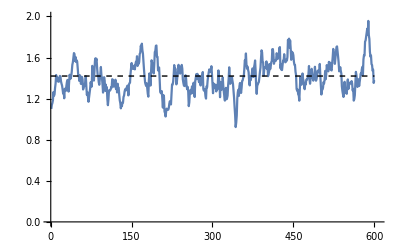

```mathematica
PriceSequenceGraph[0.0194, 1.1, 1.42, 600, 0.06]
```

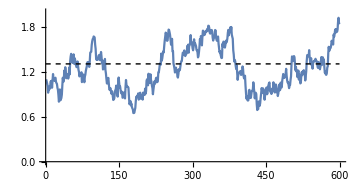
{0.0182274,2.13176,1.30662,-Graphics-}

```mathematica
cEsttStatGraph[0.0194, 1.1, 1.42, 600, 0.06, 1]
```

```mathematica
(*  Length 600 and adjustment rate 0.0194.                        *)
```

```mathematica
ctn600a0194 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 600, 0.06, 1], {i, 1, 100000}];
```

```mathematica
cEsta0194n600 = Sort[Transpose[ctn600a0194][[1]]];
```

```mathematica
Mean[cEsta0194n600]
```

0.0271665

```mathematica
tStatn600a0194 = Sort[Transpose[ctn600a0194][[2]]];
```

```mathematica
(*  The next step is to find the power of this test.  We do this    *)
(*  by finding the fraction of the simulations for which we can     *)
(*  conclude that the adjustment parameter is greater than the 5%   *)
(*  critical value. In Size.nb we found that the 5% critical value  *)
(*  is 2.90,so we look to see which t-statistics are greater than   *)
(*  2.90.                                                           *)
```

```mathematica
Length[Position[Map[Sign, tStatn600a0194- 2.90], 1]]
```

38974

```mathematica
N[Length[Position[Map[Sign, tStatn600a0194- 2.90], 1]]/Length[tStatn600a0194]]
```

0.38974

```mathematica
(*  According to Elliott, Rothenberg, and Stock, the power of a    *)
(*  test is roughly proportional to the product of the sequence    *)
(*  length 'n' and the adjustment rate'c'.  We can double the      *)
(*  adjustment rate and cut the sequence length in half or we      *)
(*  can cut the adjustment rate in half and double the sequence    *)
(*  length.  In all three cases the power should be similar.       *)
```

```mathematica
(*  Length 300 and adjustment rate 0.0388.                        *)
```

```mathematica
ctn300a0388 = ParallelTable[cEsttStat[0.0388, 1.42, 1.42, 300, 0.06, 1], {i, 1, 100000}];
```

```mathematica
cEstn300a0388 = Sort[Transpose[ctn300a0388][[1]]];
```

```mathematica
tStatn300a0388 = Sort[Transpose[ctn300a0388][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn300a0388- 2.90], 1]]/Length[tStatn300a0388]]
```

0.39621

```mathematica
(*  Length 1200 and adjustment rate 0.0097.                        *)
```

```mathematica
ctn1200a0097 = ParallelTable[cEsttStat[0.0097, 1.42, 1.42, 1200, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn1200a0097 = Sort[Transpose[ctn1200a0097][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn1200a0097 - 2.90], 1]]/Length[tStatn1200a0097]]
```

0.38102

```mathematica
(*  Length 2000 and adjustment rate 0.00582.                        *)
```

```mathematica
ctn2000a00582 = ParallelTable[cEsttStat[0.00582, 1.42, 1.42, 2000, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn2000a00582 = Sort[Transpose[ctn2000a00582][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn2000a00582 - 2.90], 1]]/Length[tStatn2000a00582]]
```

0.3771

```mathematica
(*  How will power be affected when we have 10 more years of data?   *)
```

```mathematica
(*  We can start with the estimated adjustment rate and increase     *)
(*  the sequence length to 720.                                      *)
```

```mathematica
ctn720a0194 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 720, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn720a0194 = Sort[Transpose[ctn720a0194][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn720a0194- 2.90], 1]]/Length[tStatn720a0194]]
```

0.51794

```mathematica
(*  Next we can cut the sequence length in half and double the        *)
(*  adjustment rate.                                                  *)
```

```mathematica
ctn360a0388= ParallelTable[cEsttStat[0.0388, 1.42, 1.42, 360, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn360a0388 = Sort[Transpose[ctn360a0388][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn360a0388 - 2.90], 1]]/Length[tStatn360a0388]]
```

0.52616

```mathematica
(*  Next we can cut the sequence length in half and double the        *)
(*  adjustment rate.                                                  *)
```

```mathematica
ctn1440a0097= ParallelTable[cEsttStat[0.0097, 1.42, 1.42, 1440, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn1440a0097 = Sort[Transpose[ctn1440a0097][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn1440a0097 - 2.90], 1]]/Length[tStatn1440a0097]]
```

0.5137

```mathematica
(*  The next three sets of calculations show the power         *)
(*  with 80 years (960 months) with an adjustment rate of      *)
(*  0.0194 and two variants with twice as many time periods    *)
(*  and half as many time periods.                             *)
```

```mathematica
(*  Each monthly adjustment rate is 0.0194 and there are 960   *)
(*  months.                                                    *)
```

```mathematica
ctn960a0194 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 960, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn960a0194 = Sort[Transpose[ctn960a0194][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn960a0194- 2.90], 1]]/Length[tStatn960a0194]]
```

0.76073

```mathematica
(*  Each adjustment rate is 0.0388 and there are 480 periods   *)
(*  each with a length of 2 months.                            *)
```

```mathematica
ctn480a0388 = ParallelTable[cEsttStat[0.0388, 1.42, 1.42, 480, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn480a0388= Sort[Transpose[ctn480a0388][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn480a0388- 2.90], 1]]/Length[tStatn480a0388]]
```

0.7682

```mathematica
(*  Each adjustment rate is 0.0097 and there are 1920 periods  *)
(*  each with a length of 1/2 month.                           *)
```

```mathematica
ctn1920a0097= ParallelTable[cEsttStat[0.0097, 1.42, 1.42, 1920, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn1920a0097 = Sort[Transpose[ctn1920a0097][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn1920a0097- 2.90], 1]]/Length[tStatn1920a0097]]
```

0.76273

```mathematica
(*  The next three sets of calculations show the power         *)
(*  with 100 years (1200 months) with an adjustment rate of    *)
(*  0.0194 and two variants one with twice as many time        *)
(*  periods and the other with half as many time periods.      *)
```

```mathematica
(*  Each monthly adjustment rate is 0.0194 and there are       *)
(*  1200 months.                                               *)
```

```mathematica
ctn1200a0194 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 1200, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn1200a0194 = Sort[Transpose[ctn1200a0194][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn1200a0194- 2.90], 1]]/Length[tStatn1200a0194]]
```

0.91815

```mathematica
(*  Each adjustment rate is 0.0388 and there are 600 periods   *)
(*  each with a length of 2 months.                            *)
```

```mathematica
ctn600a0388 = ParallelTable[cEsttStat[0.0388, 1.42, 1.42,600, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn600a0388= Sort[Transpose[ctn600a0388][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn600a0388- 2.90], 1]]/Length[tStatn600a0388]]
```

0.91822

```mathematica
(*  Each adjustment rate is 0.0097 and there are 2400 periods  *)
(*  each with a length of 1/2 month.                           *)
```

```mathematica
ctn1920a0097= ParallelTable[cEsttStat[0.0097, 1.42, 1.42, 2400, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn2400a0097 = Sort[Transpose[ctn1920a0097][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn2400a0097- 2.90], 1]]/Length[tStatn2400a0097]]
```

0.91921

```mathematica
(*  Does the standard deviation of the error terms affect power?   *)
```

```mathematica
ctn600a0194σ12 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 600, 0.12, 1], {i, 1, 100000}];
```

```mathematica
tStatn600a0194σ12 = Sort[Transpose[ctn600a0194σ12][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn600a0194σ12- 2.90], 1]]/Length[tStatn600a0194σ12]]
```

0.38915

```mathematica
ctn600a0194σ24 = ParallelTable[cEsttStat[0.0194, 1.42, 1.42, 600, 0.24, 1], {i, 1, 100000}];
```

```mathematica
tStatn600a0194σ24 = Sort[Transpose[ctn600a0194σ24][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn600a0194σ24- 2.90], 1]]/Length[tStatn600a0194σ24]]
```

0.38878

```mathematica
(*  The initial price affects power.  If the initial price is     *)
(*  well away from the attractor, the initial adjustment toward   *)
(*  the attractor makes the process appear to adjust more often.  *)
```

```mathematica
(*  With the initial price 1.5 times the attractor price          *)
(*  adjustment is detected much more often.                       *)
```

```mathematica
ctn600a0194po15 = ParallelTable[cEsttStat[0.0194, 2.13, 1.42, 600, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn600a0194po15 = Sort[Transpose[ctn600a0194po15][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn600a0194po15- 2.90], 1]]/Length[tStatn600a0194po15]]
```

0.5091

```mathematica
(*  With the initial price 2 times the attractor price adjustent  *)
(*  is detected more than twice as often.                         *)
```

```mathematica
ctn600a0194po2 = ParallelTable[cEsttStat[0.0194, 2.84, 1.42, 600, 0.06, 1], {i, 1, 100000}];
```

```mathematica
tStatn600a0194po2 = Sort[Transpose[ctn600a0194po2][[2]]];
```

```mathematica
N[Length[Position[Map[Sign, tStatn600a0194po2- 2.90], 1]]/Length[tStatn600a0194po2]]
```

0.82808